```mathematica
<<FunctionApproximations`
```

## Logarithm

This is the residual after the floating point byte reinterpretation

```mathematica
Solve[{ (Log[2, (1 + mx) 2^(ex)]) == (ix / L) + y, ix == (ex + B) L + mx L } // PowerExpand, y, { ex }] // FullSimplify
```

{{y→-B-mx+Log[1+mx]/Log[2]}}

```mathematica
Clear[residual];
residual[mx_] := Log[2, 1 + mx] - mx;
```

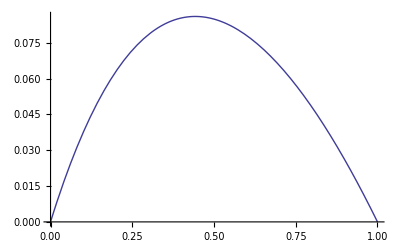

```mathematica
Plot[residual[x], { x, 0, 1 }]
```

-124.22544637-1.49803030236 mx-1.72587999/(0.352088706832+1. mx)

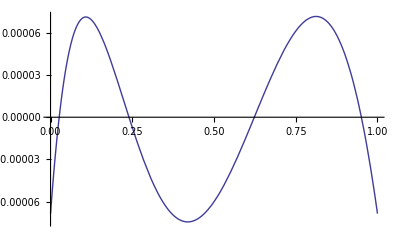

```mathematica
Clear[approx];
approx = MiniMaxApproximation[residual[x] + 1, { x, { 0, 1 }, 2, 1 }, WorkingPrecision->17] // FullSimplify // Evaluate;
-128 + approx[[2]][[1]]  /. x ->(2 mx - 1) // N[#, 17]&  // FullSimplify
Plot[(residual[x] + 1 - approx[[2]][[1]]) , { x, 0, 1 }]
```

Add this in to be more accurate for powers of 2 at the expensive of overall accuracy ...

```mathematica
1 - approx[[2]][[1]] /. x -> 0
% + (-128 + approx[[2]][[1]] /. x ->(2 mx -1)) // FullSimplify
```

-0.000068621252

-124.22551499-1.49803030236 mx-1.72587999/(0.352088706832+1. mx)

Even simpler, faster, and less accurate  ...

```mathematica
Integrate[residual[x], { x, 0, 1 }]
-127 + % // N[#, 17]&
```

(-2+Log[8])/Log[4]

-126.94269504088896

## Exponential

```mathematica
Clear[residual];
residual[z_] := 2^z - z;
```

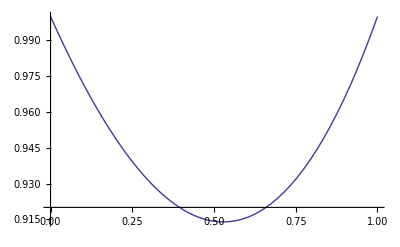

```mathematica
Plot[residual[x], { x, 0, 1 }]
```

121.27408384355+27.7280233897/(4.84252568893-1. x)-1.4901290717343 x

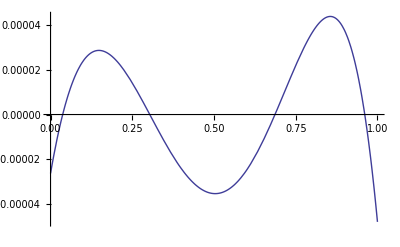

```mathematica
Clear[approx];
approx = EconomizedRationalApproximation[residual[x], { x, { 0, 1 }, 2, 1 }] // FullSimplify // Evaluate;
126 + approx // N[#, 17]&  // FullSimplify
Plot[(residual[x]- approx) , { x, 0, 1 }]
```

Add this in to be more accurate for integer powers at the expensive of overall accuracy ...

```mathematica
1 - approx /. x -> 0
% + (126 + approx) // N[#,17]& // FullSimplify
```

1-(96+(-16+Log[2]) Log[2])^2/(32 √2 (12+Log[2])^2)

121.27405755367+27.7280233897/(4.84252568893-1. x)-1.4901290717343 x

Even faster, cheaper, and less accurate ...

```mathematica
Integrate[residual[x], { x, 0 ,1 }]
126 + % // N[#, 17]&
```

-1/2+1/Log[2]

126.94269504088896

## Fast LDA Functions

### Digamma

```mathematica
Clear[psi];
psi[x_, n_] := Log[x] - 1/(2x) - Sum[BernoulliB[2k] / (2 k x^(2 k)), { k, 1, n }]
Clear[megapsi];
megapsi[x_, n_] := psi[x + 1, n] - 1 / x;
Clear[ultrapsi];
ultrapsi[x_, n_] := megapsi[x + 1, n] - 1 / x;
```

```mathematica
ultrapsi[z, 1]
% - Log[2 + z] // Together
```

-1/z-1/(1+z)-1/(12 (2+z)^2)-1/(2 (2+z))+Log[2+z]

(-48-157 z-127 z^2-30 z^3)/(12 z (1+z) (2+z)^2)

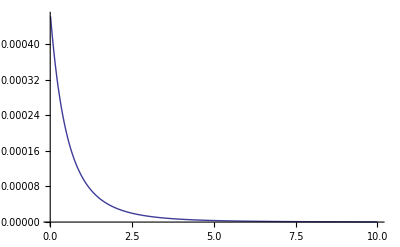

```mathematica
Plot[(PolyGamma[z] - ultrapsi[z, 1]), { z, 0.01, 10 }, PlotRange -> All]
```

### LGamma

```mathematica
Clear[lgamma];
lgamma[z_, n_] := (z - 1/2) Log[z] - z + Log[2 Pi] / 2 + Sum[BernoulliB[2k] / (2k (2k - 1) z^(2k - 1)), { k, 1, n }];
Clear[megalgamma];
megalgamma[z_, n_] := lgamma[z + 1, n] - Log[z]
Clear[ultralgamma];
ultralgamma[z_, n_] := megalgamma[z + 1, n] - Log[z]
Clear[gigalgamma];
gigalgamma[z_, n_] := ultralgamma[z + 1, n] - Log[z]
Clear[teralgamma];
teralgamma[z_, n_] := gigalgamma[z + 1, n] - Log[z]
```

```mathematica
gigalgamma[x, 1]
% // N[#, 17]&
```

-3-x+1/(12 (3+x))+1/2 Log[2 π]-Log[x]-Log[1+x]-Log[2+x]+(5/2+x) Log[3+x]

-2.0810614667953273-1. x+0.083333333333333333/(3.+x)-1. Log[x]-1. Log[1.+x]-1. Log[2.+x]+(2.5+x) Log[3.+x]

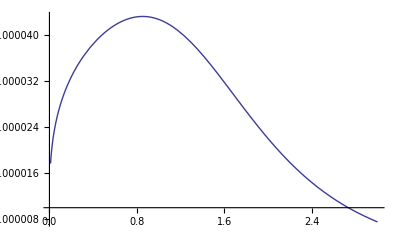

```mathematica
Plot[(gigalgamma[z, 1] - LogGamma[z]) / (1 + LogGamma[z]), { z, 0.01, 3 }, PlotRange->All]
```

## Trigonometric Functions

### Sine

#### Range Reduction

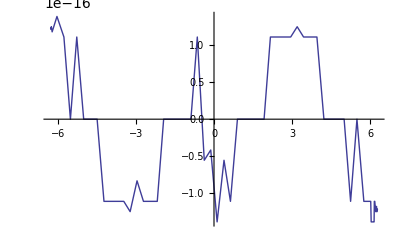

```mathematica
Plot[Sin[x] - Sign[x] Sin[Pi - Abs[x]], { x, -2 Pi, 2 Pi }]
```

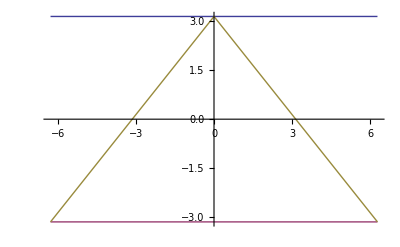

```mathematica
Plot[{ Pi, -Pi, Pi - Abs[x]}, { x, -2 Pi, 2 Pi }]
```

#### Approximation

```mathematica
Clear[qpprox];
qpprox[x_] := a x^2 + b x + c;
Clear[megaeq];
megaeq[x_] := qpprox[x] == Sin[x]
Clear[megasol];
megasol = Solve[{ megaeq[0], megaeq[Pi/2], megaeq[Pi] }, { a, b, c }] // FullSimplify // Evaluate;
Clear[ultraerr];
ultraerr = Integrate[(Sin[x] - q qpprox[x]- p qpprox[x]^2)^2 /. megasol[[1]] // FullSimplify // Evaluate, { x, 0, Pi  }] // FullSimplify // Evaluate;
Clear[ultrasol];
ultrasol = Solve[{ D[ultraerr, p] == 0, D[ultraerr, q] == 0 }]  // FullSimplify // Evaluate;
Clear[gigaerr];
gigaerr = Integrate[(Sin[x] - q qpprox[x]- p qpprox[x]^2 - r qpprox[x]^4)^2 /. megasol[[1]] // FullSimplify // Evaluate, { x, 0, Pi  }] // FullSimplify // Evaluate;
Clear[gigasol];
gigasol = Solve[{ D[gigaerr, p] == 0, D[gigaerr, q] == 0, D[gigaerr, r] == 0  }]  // FullSimplify // Evaluate;
Clear[teraerr];
teraerr = Integrate[(Sin[x] - q qpprox[x]- p qpprox[x]^2 - r qpprox[x]^4 - s qpprox[x]^6)^2 /. megasol[[1]] // FullSimplify // Evaluate, { x, 0, Pi  }] // FullSimplify // Evaluate;
Clear[terasol];
terasol = Solve[{ D[teraerr, p] == 0, D[teraerr, q] == 0, D[teraerr, r] == 0, D[teraerr, s] == 0  }]  // FullSimplify // Evaluate;
```

```mathematica
qpprox[x] /. megasol[[1]] /. x^2 -> x Abs[x]
```

(4 x)/π-(4 x Abs[x])/π^2

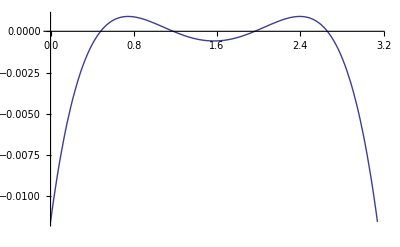

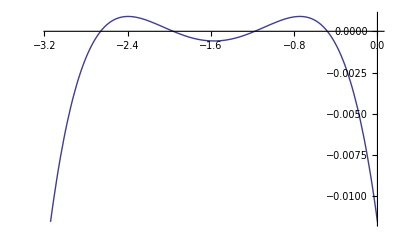

{{p→0.22308510060189463,q→0.77633023248007499}}

```mathematica
Plot[(((q qpprox[x] + p qpprox[x]^2 /. x^2 -> x Abs[x])/. megasol[[1]] /. ultrasol[[1]]) - Sin[x]) / Sin[x], { x, 0, Pi }]
Plot[(((q qpprox[x] - p qpprox[x]^2 /. x^2 -> x Abs[x])/. megasol[[1]] /. ultrasol[[1]]) - Sin[x]) / Sin[x], { x, -Pi, 0}]
ultrasol // N[#, 17]&
```

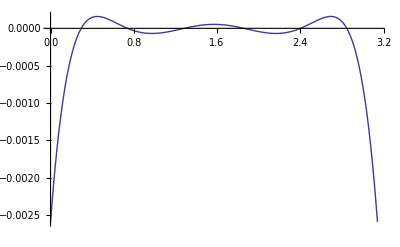

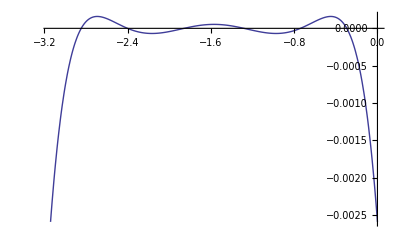

{{p→0.20725703260476271,q→0.78336492936768918,r→0.0094308905149577671}}

```mathematica
Plot[(((q qpprox[x] + p qpprox[x]^2 + r qpprox[x]^4 /. x^2 -> x Abs[x])/. megasol[[1]] /. gigasol[[1]]) - Sin[x]) / Sin[x], { x, 0, Pi }, PlotRange->All]
Plot[(((q qpprox[x] - p qpprox[x]^2 - r qpprox[x]^4 /. x^2 -> x Abs[x])/. megasol[[1]] /. gigasol[[1]]) - Sin[x]) / Sin[x], { x, -Pi, 0 }, PlotRange->All]
gigasol // N[#, 17]&
```

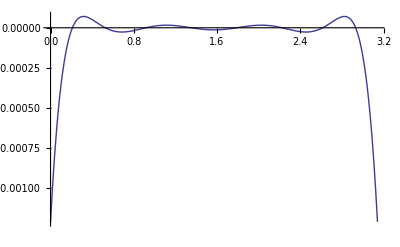

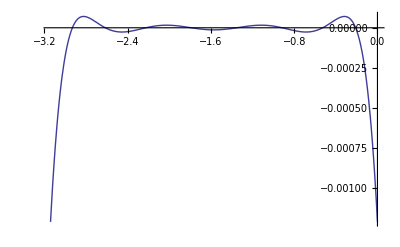

{{p→0.20363937680730309,q→0.78444488374548933,r→0.015124940802184233,s→-0.0032225901625579573}}

```mathematica
Plot[(((q qpprox[x] + p qpprox[x]^2 + r qpprox[x]^4  + s qpprox[x]^6/. x^2 -> x Abs[x])/. megasol[[1]] /. terasol[[1]]) - Sin[x]) / Sin[x], { x, 0, Pi }, PlotRange->All]
Plot[(((q qpprox[x] - p qpprox[x]^2 - r qpprox[x]^4  - s qpprox[x]^6/. x^2 -> x Abs[x])/. megasol[[1]] /. terasol[[1]]) - Sin[x]) / Sin[x], { x, -Pi, 0 }, PlotRange->All]
terasol // N[#, 17]&
```

```mathematica
qpprox[x] /. megasol[[1]]
```

(4 x)/π-(4 x^2)/π^2

### Cosine

```mathematica
Clear[qpprox];
qpprox[x_] := a x^2 + b x + c;
Clear[megaeq];
megaeq[x_] := qpprox[x] == Cos[x]
Clear[megasol];
megasol = Solve[{ megaeq[0], megaeq[Pi / 2], megaeq[Pi] }, { a, b, c }] // FullSimplify // Evaluate;
Clear[ultraerr];
ultraerr = Integrate[(Cos[x] - q qpprox[x]- p qpprox[x](1 - qpprox[x]^2))^2 /. megasol[[1]] // FullSimplify // Evaluate, { x, 0, Pi  }] // FullSimplify // Evaluate;
Clear[ultrasol];
ultrasol = Solve[{ D[ultraerr, p] == 0, q == 1 }]  // FullSimplify // Evaluate; (* Solve[{ D[ultraerr, p] == 0, D[ultraerr, q] == 0 }]  // FullSimplify // Evaluate; *)
```

```mathematica
megasol
N[%, 17]
ultrasol
N[%, 17]
```

{{a→0,b→-2/π,c→1}}

{{a→0,b→-0.63661977236758134,c→1.}}

{{p→-(7 (-720+60 π^2+π^4))/(4 π^4),q→1}}

{{p→0.54641335845679634,q→1.}}

```mathematica
1 - qpprox[x] /. megasol[[1]]
1 - qpprox[x]^2 /. megasol[[1]] // Expand
```

(2 x)/π

(4 x)/π-(4 x^2)/π^2

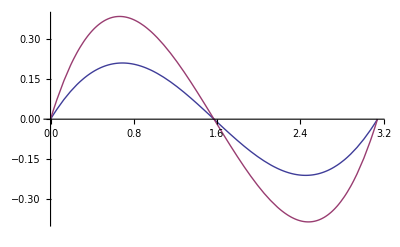

```mathematica
Plot[{ Cos[x] - qpprox[x] /. megasol[[1]], qpprox[x](1 - qpprox[x]^2)/. megasol[[1]] }, { x, 0, Pi }]
```

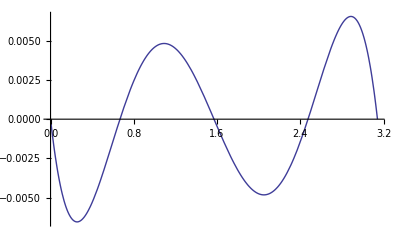

```mathematica
Plot[{ Cos[x] - q qpprox[x] - p qpprox[x] (1 - qpprox[x]^2) /. megasol[[1]] /. ultrasol[[1]]}, { x, 0, Pi}]
```

WHERE TO GO FROM HERE?  HIGHER ORDER TERM IS NOT CLEAR ...

## Erf

### Erf

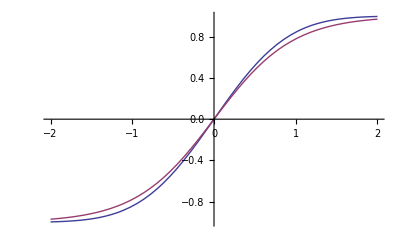

```mathematica
Plot[{ Erf[z],2 / (1 + 2^(-3 z))- 1 }, { z, -2 , 2 }]
```

```mathematica
Clear[residual];
residual[k_, x_] := Erf[x] - (1 - 2 / (1 + 2^(k x)));
objective[k_] := NIntegrate[Abs[residual[k, z] / Erf[z]], { z, -4, 4 }]
FindMinimum[objective[k], { k, 2 }, WorkingPrecision -> 17, PrecisionGoal -> 17] // Quiet
```

{0.09617036414751734,{k→3.3521449291322149}}

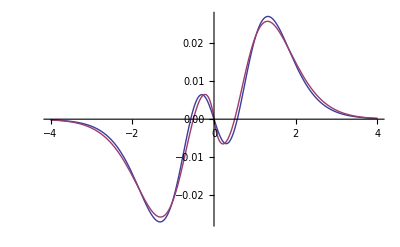

```mathematica
Plot[{ residual[k, x]  /. k -> 3.35214492913221492851588357326401031621`17., 0.07219054755431126 (15.418191568719577x^5 - x) 2^(-Abs[5.609846028328545x]) },{ x, -4, 4 }, PlotRange->All]
```

```mathematica
Clear[residapprox];
residapprox[k_, a_, b_, c_, x_]:= residual[k, x]- a (b x^5 - x) 2^(-Abs[c x]);
Clear[residobj];
residobj[k_, a_, b_, c_] := NIntegrate[(residapprox[k, a, b, c, x])^2, { x, -4, 4 }, WorkingPrecision -> 17];
FindMinimum[residobj[3.35214492913221492851588357326401031621, a, b, c], { { a, 0.0575 }, { b, 13.11 },{ c, 4.4 } }, Method->"PrincipalAxis"]// Quiet
```

{9.50831×10^-6,{a→0.0721905,b→15.4182,c→5.60985}}

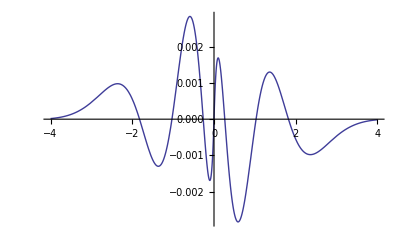

```mathematica
Plot[{ (residual[k, x]  /. k -> 3.35214492913221492851588357326401031621`17.) -0.07219054755431126 (15.418191568719577x^5 - x) 2^(-Abs[5.609846028328545x]) },{ x, -4, 4 }, PlotRange->All]
```

Better, but more expensive to evaluate ...

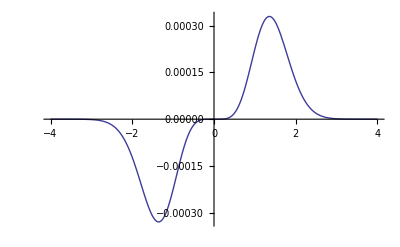

```mathematica
Plot[(Sign[x] Sqrt[1 - Exp[-x^2 (4/Pi + a x^2) /(1 + a x^2)]] /. a -> 8 (Pi - 3)/(3 Pi (4 - Pi))) - Erf[x], { x, -4, 4 }]
```

### InverseErf

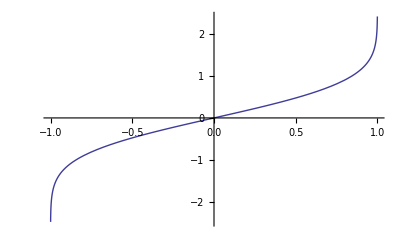

```mathematica
Plot[InverseErf[x], { x, -1, 1 }]
```

```mathematica
Solve[erfx == (1 - 2 / (1 + 2^(k x))), x] // FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[-(1+erfx)/(-1+erfx)]/(k Log[2])}}

```mathematica
Clear[residual];
residual[k_, x_] := InverseErf[x] - k Log[2, (1 + x) / (1 - x)];
objective[k_] := NIntegrate[Abs[residual[k, z] / Erf[z]], { z, -0.9, 0.9 }]
FindMinimum[objective[k], { k, 3 }, WorkingPrecision -> 17, PrecisionGoal -> 17]// Quiet
```

{0.044605008521913403,{k→0.30004578719350504}}

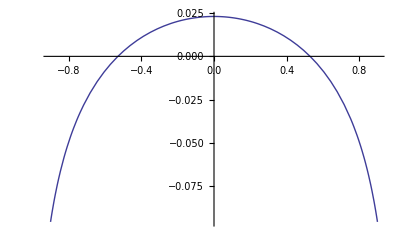

```mathematica
Plot[(InverseErf[x] - k Log[2, (1 + x) / (1 - x)]) / InverseErf[x] /. k -> 0.30004578719350504, { x, -0.9, 0.9 }, PlotRange->All]
```

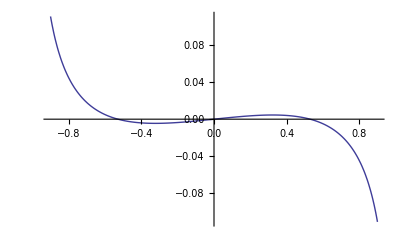

```mathematica
Plot[(InverseErf[x] - k Log[2, (1 + x) / (1 - x)])/. k -> 0.30004578719350504, { x, -0.9, 0.9 }, PlotRange->All]
```

(0.0202879 x+0. x^2-0.0723689 x^3)/(0.991303+0. x-0.805978 x^2+0. x^3)

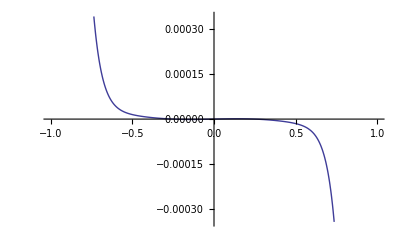

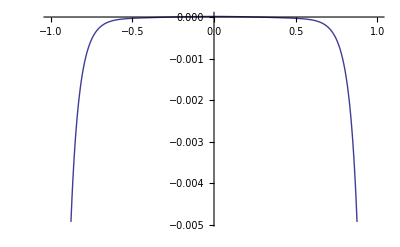

```mathematica
Clear[megaprox];
megaprox = EconomizedRationalApproximation[(InverseErf[x] - k Log[2, (1 + x) / (1 - x)])/. k -> 0.30004578719350504, { x, { -1, 1 }, 3, 3 }]
Plot[((InverseErf[x] - k Log[2, (1 + x) / (1 - x)])/. k -> 0.30004578719350504) - megaprox, { x, -1, 1 }]
Plot[(((InverseErf[x] - k Log[2, (1 + x) / (1 - x)])/. k -> 0.30004578719350504) - megaprox) / InverseErf[x], { x, -1, 1 }]
```

## Lambert W

### Original Recipe

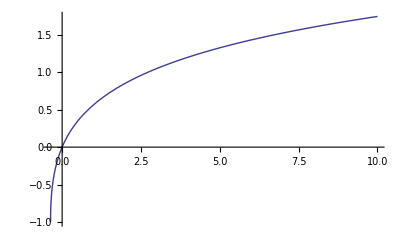

```mathematica
Plot[ProductLog[x], { x, -1/E, 10 }]
```

General strategy ... approximation followed by Halley' s method cleanup (or Newton if feeling miserly)

```mathematica
Clear[householder];
householder[d_, f_] := x + d D[(1/f[x]), { x, d - 1 }] / D[(1/f[x]), { x, d }];
Clear[lambnewt];
lambnewt[x_, z_] := householder[1, (#1 Exp[#1] - z)&] // FullSimplify // Evaluate;
Clear[lambhal];
lambhal[x_, z_] := householder[2, (#1 Exp[#1] - z)&] // FullSimplify // Evaluate;
```

```mathematica
lambnewt[w, z]
lambhal[w, z]
Expand/@ ({ Numerator[#], Denominator[#]}& [lambhal[w, x]])
% /. ⅇ^w w -> z /. ⅇ^w w^2 -> w z /. ⅇ^w w^3 -> w^2 z // Collect[#, w]&
% /. x + z -> p /. 2 x + 2 z -> 2 p
```

(w^2+ⅇ^-w z)/(1+w)

(ⅇ^w w^3+(2+w (4+w)) z)/(ⅇ^w (2+w (2+w))+(2+w) z)

{ⅇ^w w^3+2 x+4 w x+w^2 x,2 ⅇ^w+2 ⅇ^w w+ⅇ^w w^2+2 x+w x}

{2 x+4 w x+w^2 (x+z),2 ⅇ^w+2 x+2 z+w (x+z)}

{p w^2+2 x+4 w x,2 ⅇ^w+2 p+p w}

Look for approximation with the same structure as the asymptotic approximation ...

```mathematica
Clear[data];
data = Table[{ x, ProductLog[x] }, { x, -1/E, 1, 1/50 }];
Clear[model];
model = NonlinearModelFit[data // N[#, 17]&, { a + Log[c (x + 1/E) + d] - Log[Log[c (x + 1/E) + d]] + Log[Log[c (x + 1/E) + d]] / Log[c (x + 1/E) + d], c > 0, d > 1}, { { a, -1 }, { c, 1.5 }, { d, 3 } }, x, WorkingPrecision -> 17] // Quiet ;
model["BestFitParameters"] //Quiet
model // Normal /. Log[x_] -> log2[x] / Log[2] // N[#, 17]& // Simplify // Quiet
```

{a→-0.73776996948790008,c→1.5468655571982242,d→1.6813068050362248}

-0.73776996948790008+Log[2.250366841785659+1.5468655571982242 x]+Log[Log[2.250366841785659+1.546865557198224 x]]/Log[2.250366841785659+1.5468655571982242 x]-1. Log[Log[2.250366841785659+1.5468655571982242 x]]

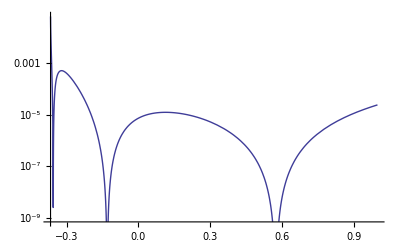

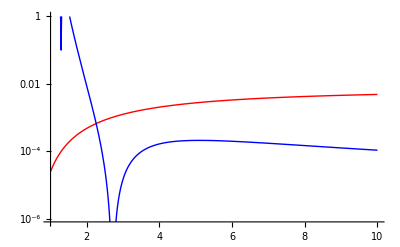

```mathematica
LogPlot[{ Abs[ProductLog[x] - lambhal[model // Normal, x]]},{ x, -1/E, 1 }] // Quiet
LogPlot[{ Abs[ProductLog[x] - lambhal[model // Normal, x]],
Abs[ProductLog[x] - lambhal[Log[x] - Log[Log[x]] + Log[Log[x]] / Log[x], x]] },{ x, 1.01, 10 }, PlotStyle -> { Red, Blue }] // Quiet
```

Find the point where the asymptotic formula is better ...

```mathematica
FindRoot[(model // Normal) == Log[x] - Log[Log[x]] + Log[Log[x]] / Log[x], { x, 3 }] // Quiet
```

{x→2.26445}

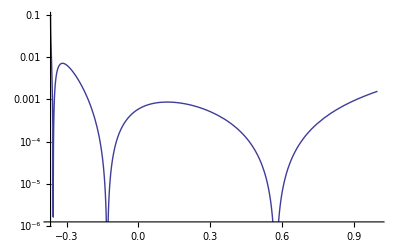

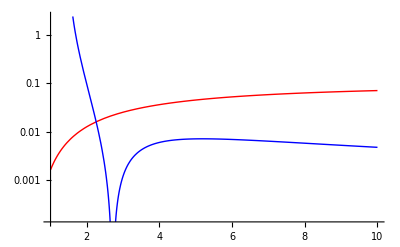

```mathematica
LogPlot[{ Abs[ProductLog[x] - lambnewt[model // Normal, x]]},{ x, -1/E, 1 }] // Quiet
LogPlot[{ Abs[ProductLog[x] - lambnewt[model // Normal, x]],
Abs[ProductLog[x] - lambnewt[Log[x] - Log[Log[x]] + Log[Log[x]] / Log[x], x]] },{ x, 1.01, 10 }, PlotStyle -> { Red, Blue }] // Quiet
```

### W[Exp[x]]

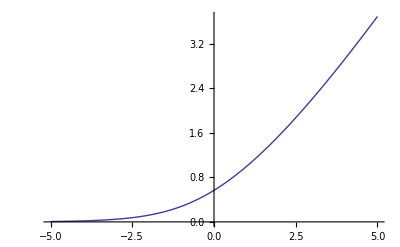

```mathematica
Plot[ProductLog[Exp[x]], { x, -5, 5 }]
```

```mathematica
Clear[householder];
householder[d_, f_] := x + d D[(1/f[x]), { x, d - 1 }] / D[(1/f[x]), { x, d }];
Clear[explambnewt];
explambnewt[x_, z_] := householder[1, (Log[#1 Exp[#1]] - z)&] // PowerExpand // FullSimplify // Evaluate;
Clear[explambhal];
explambhal[x_, z_] := householder[2, (Log[#1 Exp[#1]] - z)&] // PowerExpand // FullSimplify // Evaluate;
```

```mathematica
explambnewt[w, x]
explambhal[w, x] // FullSimplify
{ Numerator[%] // Collect[#, w]&, Denominator[%] // Collect[#, w]& }
% /. x -> p + Log[w] // Simplify
```

(w (1+x-Log[w]))/(1+w)

(w (2+x+w (3+2 x)-(1+2 w) Log[w]))/(2+w (5+2 w)-x+Log[w])

{w^2 (3+2 x-2 Log[w])+w (2+x-Log[w]),2+5 w+2 w^2-x+Log[w]}

{w (2+p+3 w+2 p w),2-p+5 w+2 w^2}

Asymptotic Approximation ...

```mathematica
Log[y] - Log[Log[y]] + Log[Log[y]] / Log[y] /. y -> Exp[x] // PowerExpand // FullSimplify
Limit[ProductLog[Exp[x]] - %, x -> Infinity]
```

x+(-1+1/x) Log[x]

0

```mathematica
Clear[megaprox];
megaprox[x_] := (Max[x, k]  - Log[Max[x, k]] + Log[Max[x, k]] / Max[x, k]) 2^(a (Min[x, k] - k));
Clear[data];
data = Table[{ x, ProductLog[Exp[x]] }, { x, -4, 4, 0.1 }];
Clear[model];
model = NonlinearModelFit[data // N[#, 17]&, { megaprox[x], a > 0, k > 0 }, { { k, 1 }, { a, 1 } }, x, WorkingPrecision -> 17] // Quiet;
model["BestFitParameters"] // Quiet
```

{k→1.1765631308929415,a→0.94537622167837827}

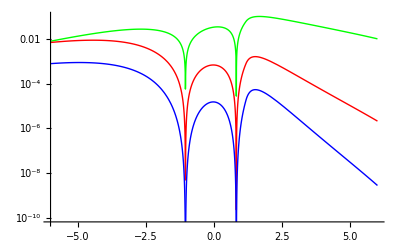

```mathematica
LogPlot[{ Abs[ProductLog[Exp[x]] - ( model // Normal)],Abs[ProductLog[Exp[x]] - explambnewt[model // Normal, x]],
Abs[ProductLog[Exp[x]] - explambhal[model // Normal, x]] }, { x, -6, 6 }, PlotStyle -> { Green, Red, Blue, Orange }] // Quiet
```

```mathematica
Limit[ProductLog[Exp[x]] - Log[(1 + Exp[x]) / x], x -> Infinity]
```

0